```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
SpinWeightedSpheroidalHarmonicS[1,1,1,0.1,Method->{"SphericalExpansion","NumTerms"->6}]["ExpansionCoefficients"]
```

<|1→0.999806,2→-0.0196779,3→0.000351223,4→-4.16333×10^-6,5→4.28527×10^-8,6→-3.48923×10^-10,7→2.53225×10^-12|>

```mathematica
(*<0,1,0|sin(θ)|-120>*)
```

```mathematica
InnerProductOverSinIntegral[l_,lp_, m_,sp_]:=Integrate[Conjugate[SpinWeightedSphericalHarmonicY[0,lp,m,θ,ϕ]]Sin[θ] SpinWeightedSphericalHarmonicY[sp,l,m,θ,ϕ] Sin[θ], {θ,0,π},{ϕ,0,2π}]
```

## Calculating projection coefficients

```mathematica
sphericalExpansion[l_,m_,γ_?NumericQ,θ_,ϕ_]:=
Module[{coefs,n=20},
coefs = SpinWeightedSpheroidalHarmonicS[1,l,m,γ,Method->{"SphericalExpansion","NumTerms"->n}]["ExpansionCoefficients"];
Sum[coefs[[i]]SpinWeightedSphericalHarmonicY[1,i,m,θ,ϕ],{i,Max[1,Abs[m]],n}]
]
```

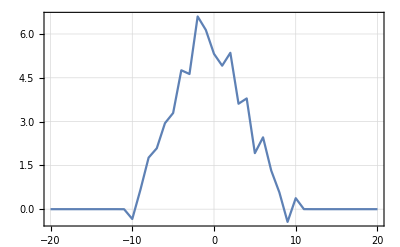

```mathematica
Module[{error,l=20,γ=0.1, θ=π/2, ϕ=0},
error[m_]:= (Abs[SpinWeightedSpheroidalHarmonicS[1,l,m,γ][θ,ϕ]-sphericalExpansion[l,m,γ,θ,ϕ]])/Abs[SpinWeightedSpheroidalHarmonicS[1,l,m,γ][θ,ϕ]];
data =Table[{m,Log10[error[m]]},{m,-l,l}];
ListLinePlot[data, Frame->True, GridLines->Automatic]
]
```

```mathematica
data
```

{{-20,1.},{-19,1.},{-18,1.},{-17,1.},{-16,1.},{-15,1.},{-14,1.},{-13,1.},{-12,1.},{-11,1.00001},{-10,1.00002},{-9,0.707835},{-8,9.25024},{-7,50.0592},{-6,1886.67},{-5,6105.76},{-4,161281.},{-3,1.52054×10^6},{-2,1.13426×10^7},{-1,2.51109×10^7},{0,1.3533×10^7},{1,2.66204×10^6},{2,502325.},{3,63156.9},{4,9355.31},{5,1332.52},{6,96.7645},{7,17.2705},{8,0.151483},{9,0.987409},{10,1.},{11,1.},{12,1.},{13,1.},{14,1.},{15,1.},{16,1.},{17,1.},{18,1.},{19,1.},{20,1.}}

```mathematica
sphericalExpansion[1,1,0.1,π/2,0]
```

-0.238016

```mathematica
SpinWeightedSpheroidalHarmonicS[1,1,1,0.1][π/2,0]
```

-0.238016

```mathematica
Log[Abs[%33 - %32]/%33]
```

-1.11022×10^-16

```mathematica
b[s_,l_,lp_,m_,γ_?NumericQ]:= NIntegrate[Sin[θ]SpinWeightedSpheroidalHarmonicS[s,l,m, γ][θ,ϕ]Conjugate[SpinWeightedSphericalHarmonicY[s, lp,m, θ, ϕ]], {θ,0,π},{ϕ,0,2π}]
```

```mathematica
b[1,1,1,1,0.1]
```

0.999806

```mathematica
MysphericalExpansion[s_,l_,m_,γ_?NumericQ,θ_,ϕ_]:=
Module[{coefs,n=5},
coefs = Table[b[s, l,j,m,γ],{j,Max[{Abs[s], Abs[m]}], n}];
Print[coefs];
Sum[coefs[[i]]SpinWeightedSphericalHarmonicY[s,i,m,θ,ϕ],{i,Max[Abs[s],Abs[m]],n}]
]
```

```mathematica
CheckBsError[s_,l_, m_,γ_?NumericQ, n_]:=Module[{},
bs = Table[b[s, l , j , m , γ], {j, Max[{Abs[s], Abs[m]}], n}];
coefs=SpinWeightedSpheroidalHarmonicS[s,l,m,γ,Method->{"SphericalExpansion","NumTerms"->n}]["ExpansionCoefficients"];
error = Table[Abs[bs[[i]]-coefs[[i]]], {i, 1, n}];j
data = Table[{j, Log[10,error[[j]]]},{j,1,n}];
ListLinePlot[data]
]
```

```mathematica
data
```

{{1,-23.5924},{2,-28.3004},{3,-31.3378},{4,-38.8575},{5,-38.6977},{6,-38.402}}

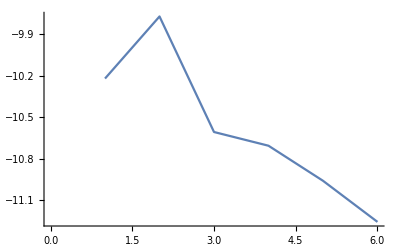

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.53973×10^-10 and 7.579195259525618`*^-16 for the integral and error estimates.

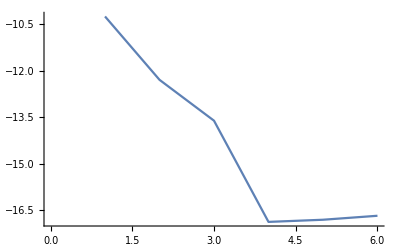

```mathematica
CheckBsError[1,2,1,0.9, 6]
```

```mathematica
error
```

{5.67497×10^-11,5.12031×10^-13,2.45554×10^-14,1.33171×10^-17,1.56251×10^-17,2.10004×10^-17}

```mathematica
bs
```

{0.99975,-0.0223669,0.000427703,-5.21821×10^-6,5.50537×10^-8,-4.53973×10^-10}

```mathematica
Log[10,Abs[bs[[1]]-coefs[[1]]]]
```

-12.2575

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.53973×10^-10 and 7.5792×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.33669×10^-12 and 1.37922×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.05815×10^-14 and 2.63957×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

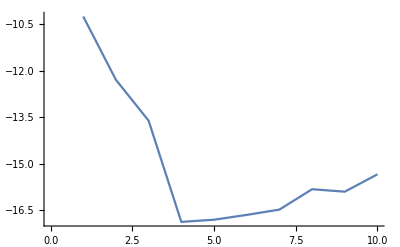

```mathematica
CheckBsError[1,1,0,0.1, 10]
```

```mathematica
data
```

{{1,-10.246},{2,-12.2908},{3,-13.6099},{4,-16.8762},{5,-16.8059},{6,-16.6503},{7,-16.4794},{8,-15.8217},{9,-15.901},{10,-15.3404}}

```mathematica
bs
```

{0.99975,-0.0223669,0.000427703,-5.21821×10^-6,5.50537×10^-8,-4.53973×10^-10,3.33669×10^-12,-2.05815×10^-14,-8.34836×10^-18,-4.57262×10^-16}

```mathematica
coefs
```

<|1→0.99975,2→-0.0223669,3→0.000427703,4→-5.21821×10^-6,5→5.50537×10^-8,6→-4.53973×10^-10,7→3.33673×10^-12,8→-2.07323×10^-14,9→1.17247×10^-16,10→-5.84042×10^-19,11→2.68716×10^-21|>

```mathematica
(*Pretty mych identical up to 9th dp*)
```

## Projecting Spheroidal Harmonics onto Spherical Harmonics

```mathematica
mixingCoefs[sp_,l_,lp_, m_]:= -sp  Sqrt[(2(2l+1))/(2 lp +1)]ClebschGordan[{l,m},{1,0},{lp,m}] ClebschGordan[{l,-sp} ,{1,sp }, {lp ,0}]
```

```mathematica
tmp=SpinWeightedSpheroidalHarmonicS[1,2,2,0.9,Method->{"SphericalExpansion","NumTerms"->10}]["ExpansionCoefficients"]
2/.tmp
```

<|2→0.991975,3→-0.125425,4→0.0159106,5→-0.00136567,6→0.000107669,7→-6.7635×10^-6,8→3.91181×10^-7,9→-1.92908×10^-8,10→8.83711×10^-10,11→-3.58201×10^-11,12→1.35979×10^-12|>

0.991975

```mathematica
sinS[s_,l_,m_,γ_?NumericQ, n_, θ_,ϕ_]:= Module[{bs, ss},
bs = SpinWeightedSpheroidalHarmonicS[s,l,m,γ,Method->{"SphericalExpansion","NumTerms"->n}]["ExpansionCoefficients"];
Sum[(j/.bs)*mixingCoefs[s,j,k,m] SpinWeightedSphericalHarmonicY[0,k,m,θ,ϕ],{j,Max[{Abs[s], Abs[m]}], n}, {k,j-1,j+1}]
]
```

```mathematica
ParallelEvaluate[Off[ClebschGordan::tri]]
Off[ClebschGordan::tri]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{0,1}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=0, m=-1

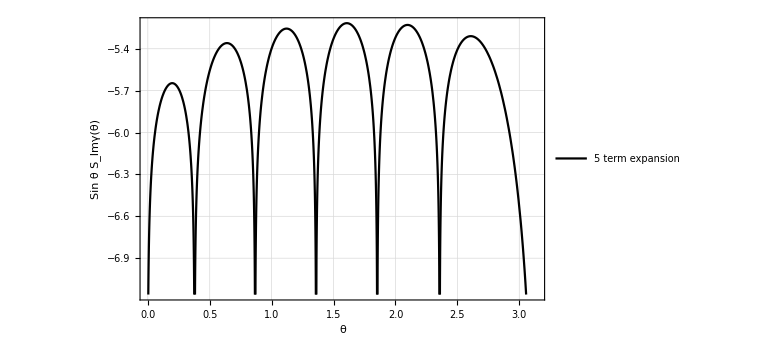

```mathematica
Module[{bs,sum, s=1, l=1,m=-1,γ=0.9, n=5, ϕ=0},
bs=SpinWeightedSpheroidalHarmonicS[s,l,m,γ,Method->{"SphericalExpansion","NumTerms"->n}]["ExpansionCoefficients"];
sum =Sum[(j/.bs)*mixingCoefs[s,j,k,m] SpinWeightedSphericalHarmonicY[0,k,m,θ,ϕ],{j,Max[{Abs[s], Abs[m]}], n}, {k,j-1,j+1}];

Plot[{Log10[Abs[sum-Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]]]}, {θ,0,π}, PlotStyle->{Black}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{ n "term expansion", "BHPTk"} , GridLines->Automatic, ImageSize->Large]
]
```

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{0,1}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=0, m=-1

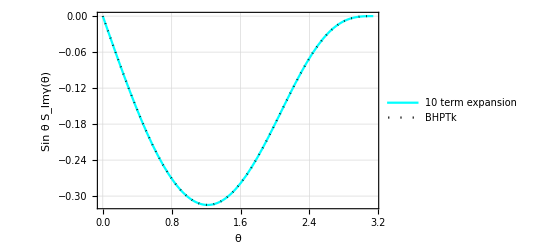

```mathematica
With[{s=1, l=1,m=-1,γ=0.9, n=10, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,0},{1,2}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=-2

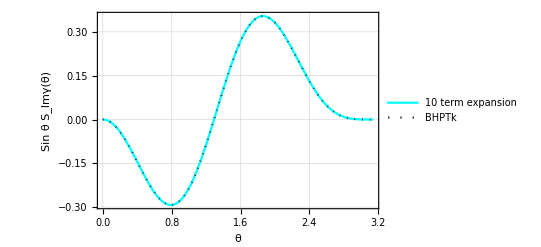

```mathematica
With[{s=1, l=3,m=-2,γ=0.9, n=10, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

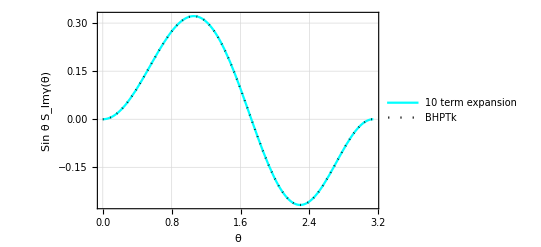

```mathematica
With[{s=1, l=2,m=0,γ=0.9, n=10, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,0},{0,-1}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=0, m=1

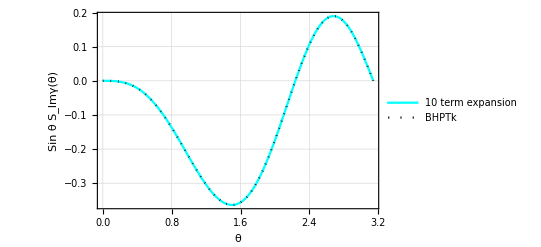

```mathematica
With[{s=1, l=2,m=1,γ=0.9, n=10, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,0},{1,-2}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

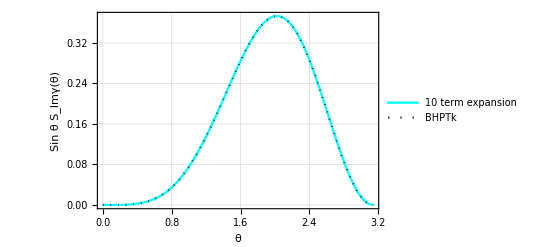

```mathematica
With[{s=1, l=2,m=2,γ=0.9, n=10, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,0},{1,-2}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

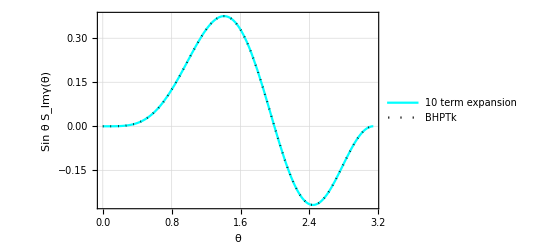

```mathematica
With[{s=1, l=3,m=2,γ=0.9, n=10, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

```mathematica
With[{s=1, l=3,m=2,γ=0.9, n=20, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,0},{1,-2}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

-Graphics-

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,0},{1,-2}] is not physical.

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=0, l=1, m=2

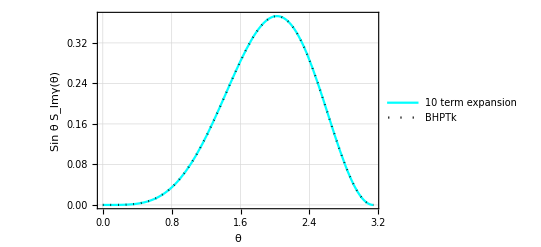

```mathematica
With[{s=1, l=2,m=2,γ=0.9, n=5, ϕ=0},
Plot[{sinS[s,l,m,γ,  n, θ,ϕ], Sin[θ] SpinWeightedSpheroidalHarmonicS[s, l,m, γ][θ,ϕ]}, {θ,0,π}, PlotStyle->{Cyan, {Black, Dotted}}, Frame->True,FrameLabel->{"θ" , "Sin θ S_lmγ(θ)"}, PlotLegends->{"10 term expansion", "BHPTk"} , GridLines->Automatic]
]
```

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
g=ToMetric["Kerr"]
```

g_αβ^

```mathematica
g[-t,-t]
```

(-a^2+2 M r-r^2+a^2 Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)

```mathematica
Solve[{-Ε ==g[-t,-t] tdot + g[-t,-ϕ] phidot, L== g[-ϕ,-t] tdot + g[-ϕ,-ϕ]  phidot},{tdot, phidot}]//FullSimplify
```

{{tdot→Ε+(4 M r (-a L+(a^2+r^2) Ε))/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ])),phidot→(-2 a (a L-2 M r Ε)+2 L (a^2+r (-2 M+r)) Csc[θ]^2)/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]))}}

```mathematica
Integrate[Log[1+x],x]
```

-x+Log[1+x]+x Log[1+x]

```mathematica
DSolve[{D[((1+x)u''[x]),{x,2}] == -8 Sin[2x] - 8(1+x)Cos[2x], u[0]==1, u'[0]==-1, -((1+π)u''[π])== -2-2π, ((1+π)u''[π])' == 2},,u[x], {x,0,π}]
```

DSolve::deqx: Supplied equations are not differential or integral equations of the given functions.

DSolve[{2 u^(3)[x]+(1+x) u^(4)[x]==-8 (1+x) Cos[2 x]-8 Sin[2 x],u[0]==1,u'[0]==-1,-((1+π) u''[π])==-2-2 π,((1+π) u''[π])'==2},Null,u[x],{x,0,π}]